```mathematica
lum = 10;
sqrtsbin = Table[350 + 25*i, {i,0,400}];
thetaList=Table[(Pi/72)*i,{i,1,71}];
factor=0.3894*10^15;
sqrtsbinnew = Table[350 + 50*i, {i,0,200}];
br = 72/81
```

8/9

```mathematica
SetDirectory[NotebookDirectory[]];
ww00= Get["cosine_bin_ww00.dat"];
ww10 = Get["cosine_bin_ww10.dat"];
```

```mathematica
ww01 = Get["cosine_bin_ww01.dat"];
```

```mathematica
ww0m1 = Get["cosine_bin_ww0m1.dat"];
wwm10 = Get["cosine_bin_wwm10.dat"];
```

```mathematica
ww11 = Get["cosine_bin_ww11.dat"];
wwm1m1 = Get["cosine_bin_wwm1m1.dat"];
ww1m1 = Get["cosine_bin_ww1m1.dat"];
wwm11 = Get["cosine_bin_wwm11.dat"];
sumww =( ww00 + ww10  + ww01 + ww0m1  + wwm10  + ww11  + wwm1m1 + ww1m1  + wwm11)* lum* factor*br   ;
```

```mathematica
zz00= Get["cosine_bin_zz00.dat"];
zz10 = Get["cosine_bin_zz10.dat"];
zz01 = Get["cosine_bin_zz01.dat"];
zz0m1 = Get["cosine_bin_zz0m1.dat"];
zzm10 = Get["cosine_bin_zzm10.dat"];
zz11 = Get["cosine_bin_zz11.dat"];
zzm1m1 = Get["cosine_bin_zzm1m1.dat"];
zz1m1 = Get["cosine_bin_zz1m1.dat"];
zzm11 = Get["cosine_bin_zzm11.dat"];
```

```mathematica
sumzz = (zz00 + zz10  + zz01 + zz0m1  + zzm10  + zz11  + zzm1m1 + zz1m1  + zzm11)* lum* factor *br ;
```

```mathematica
pp11 = Get["cosine_bin_pp11.dat"];
ppm1m1 = Get["cosine_bin_ppm1m1.dat"];
pp1m1 = Get["cosine_bin_pp1m1.dat"];
ppm11 = Get["cosine_bin_ppm11.dat"];
```

```mathematica
sumpp =   (pp11  + ppm1m1 + pp1m1  + ppm11 )* lum* factor*br ;
```

```mathematica
sumpp[[400,73]]
```

-0.118476

```mathematica
zpm10 = Get["cosine_bin_zpm10.dat"];
zp10 = Get["cosine_bin_zp10.dat"];
zp11 = Get["cosine_bin_zp11.dat"];
zpm1m1 = Get["cosine_bin_zpm1m1.dat"];
zp1m1 = Get["cosine_bin_zp1m1.dat"];
zpm11 = Get["cosine_bin_zpm11.dat"];
sumzp = ( zp10+zpm10+ zp11  + zpm1m1 + zp1m1  + zpm11)* lum* factor *br ;

dytww00 =  Get["dyt015_cosine_bin_ww00.dat"];
dytww11 =  Get["dyt015_cosine_bin_ww11.dat"];
dytwwm1m1 =  Get["dyt015_cosine_bin_wwm1m1.dat"];
```

```mathematica
dytzz00 =  Get["dyt015_cosine_bin_zz00.dat"];
dytzz11 =  Get["dyt015_cosine_bin_zz11.dat"];
dytzzm1m1 =  Get["dyt015_cosine_bin_zzm1m1.dat"];
```

```mathematica
dytsumww = (dytww00 + ww10  + ww01 + ww0m1  + wwm10  + dytww11  + dytwwm1m1 + ww1m1  + wwm11) * lum* factor *br;
dytsumzz = (dytzz00 + zz10  + zz01 + zz0m1  + zzm10  + dytzz11  + dytzzm1m1 + zz1m1  + zzm11 )* lum* factor*br;
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
sumwwtable = Table[{sqrtsbin[[k]],sumzz[[k,j]]+ sumww[[k,j]]+sumpp[[k,j]]+ sumzp[[k,j]]},{k,1,Length@sqrtsbin},{j,2,72}];

intsumww =Table[ Interpolation[sumwwtable [[All, j ]]],{j,1,71} ];
```

```mathematica
sumzztable = Table[{sqrtsbin[[k]],dytsumzz[[k,j]]+ dytsumww[[k,j]]+sumpp[[k,j]]+ sumzp[[k,j]]},{k,1,Length@sqrtsbin},{j,2,72}];

intsumzz =Table[ Interpolation[sumzztable [[All, j ]]],{j,1,71} ];
```

```mathematica
low=5000;
high=10000;
```

```mathematica
dytintbkg =Table[NIntegrate[lum*intsumww [[i]][en]  ,{en,low,high}],{i,1,71}];
dytintsgbks =Table[NIntegrate[lum*intsumzz [[i]][en] ,{en,low,high}],{i,1,71}];
```

```mathematica
thetaList1=Table[(Pi/72)*i,{i,1,71}];

sumall = Table[{thetaList1[[k]],dytintbkg[[k]]},{k,1,71}];
sumsigback = Table[{thetaList1[[k]],dytintsgbks[[k]]},{k,1,71}];
```

```mathematica
sum =  Interpolation[sumall]
sumsb=  Interpolation[sumsigback ]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
numberbins = 10;

thetabins =Table[N[ArcCos[1- i 2/numberbins]],{i,0,numberbins}]
```

{0.,0.643501,0.927295,1.15928,1.36944,1.5708,1.77215,1.98231,2.2143,2.49809,3.14159}

```mathematica
thetabins [[1]] = 10*Pi/180
thetabins [[Length@thetabins]] = Pi - 10*Pi/180
```

π/18

(17 π)/18

```mathematica
thetabins
```

{π/18,0.643501,0.927295,1.15928,1.36944,1.5708,1.77215,1.98231,2.2143,2.49809,(17 π)/18}

```mathematica
totalbinned = Table[NIntegrate[Sin[θ]sum[θ], {θ,thetabins[[j]],thetabins[[j+1]]}],{j,1,Length@thetabins-1}];
totalbinnedsb = Table[NIntegrate[Sin[θ]sumsb[θ], {θ,thetabins[[j]],thetabins[[j+1]]}],{j,1,Length@thetabins-1}];
```

```mathematica
background = totalbinned;
signal  = totalbinnedsb  - totalbinned
```

{0.517306,0.435209,0.415115,0.405632,0.399864,0.396327,0.395025,0.39746,0.410585,0.489152}

```mathematica
chi = signal/Sqrt[background]
```

{0.0237282,0.0383759,0.0461739,0.0490438,0.0476791,0.0432703,0.0370771,0.0299801,0.0222863,0.0128767}

```mathematica
thetabins1 =Table[N[ArcCos[1- i 2/numberbins]],{i,0,numberbins}]
```

{0.,0.643501,0.927295,1.15928,1.36944,1.5708,1.77215,1.98231,2.2143,2.49809,3.14159}

```mathematica
totaltable = Table[{-Cos[thetabins1[[k]]],chi [[k]] }, {k,1,Length@thetabins1-1}];
totaltable500010000= Join[totaltable,{{-Cos[thetabins1[[Length@thetabins1]]],chi[[Length@thetabins1-1]]}}]
```

{{-1.,0.0237282},{-0.8,0.0383759},{-0.6,0.0461739},{-0.4,0.0490438},{-0.2,0.0476791},{-6.12323×10^-17,0.0432703},{0.2,0.0370771},{0.4,0.0299801},{0.6,0.0222863},{0.8,0.0128767},{1.,0.0128767}}

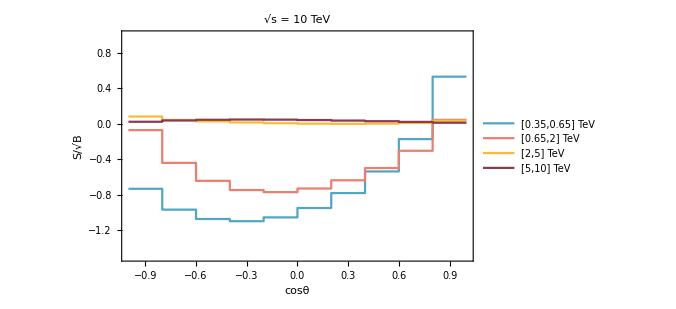

```mathematica
lineplot=ListPlot[{totaltable350650,totaltable6502000,totaltable20005000,totaltable500010000},Joined->True,InterpolationOrder->0,PlotStyle->{ColorData[colorselecitonumber][5],ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][15]},Frame->True,Axes->False,FrameLabel->{Style[DisplayForm["cosθ"],Black,19,FontFamily->"Times"],Style["S/√B",Black,17,FontFamily->"Times"]},
PlotLegends->{Placed[LineLegend[{Style["[0.35,0.65] TeV",Black,15,FontFamily->"Times"],Style["[0.65,2] TeV",Black,15,FontFamily->"Times"],Style["[2,5] TeV",Black,15,FontFamily->"Times"],Style["[5,10] TeV",Black,15,FontFamily->"Times"]},LegendLayout->{"Row",3}],{{0.35,0.82},{0.25,0.3}}]},
(*PlotLegends->{Placed[{Style["[0.35,0.65] TeV",Black,15,FontFamily->"Times"],Style["[0.65,2] TeV",Black,15,FontFamily->"Times"]},{0.3,0.87}],Placed[{Style["[2,5] TeV",Black,15,FontFamily->"Times"],Style["[5,10] TeV",Black,15,FontFamily->"Times"]},{0.7,0.87}]},*)
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",10 TeV} ],Black,18,FontFamily->"Times"],
PlotRange->{{-1,1},{-1.5,1}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
```

```mathematica
Export["signal_sens_10TeV.pdf",lineplot]
```

signal_sens_10TeV.pdf